# Transient

```mathematica
(*************************************** Analytical expressions ***************************************)

(*
Abbreviations:
k = k_C^- and kc = k_C^+
A = A_C and B = D_C
*)

k=A*B; kc=B-k; 
Id=({{1, 0}, {0, 1}}); km=({{-kc, k}, {kc, -k}}); Iv=({{1}, {0}}); Ret=({{r, 0}, {0, 0}}); Rem=({{r, 0}}); (*Useful matrices*)

dlsv0=Inverse[(s*Id-km)].Iv; (*Subscript[ΔL^(->), s]^(0): Eq. S12 with x=0 *)
dlsv1=Inverse[(s*Id-km)].Ret.dlsv0; (*Subscript[ΔL^(->), s]^(1): Eq. S12 with x=1 *)

dls=1/s*Rem.dlsv0; (* <Subscript[ΔL, s]^1>: Eq. S8 with n=1 *)
dl2s=1/s*Rem.dlsv0+2/s*Rem.dlsv1; (* <Subscript[ΔL, s]^2>: Eq. S8 with n=2 *)

dltm=InverseLaplaceTransform[dls,s,t]; (* <Subscript[ΔL, t]>: Eq. S13 with n=1 *)
dl2tm=InverseLaplaceTransform[dl2s,s,t];(* <Subscript[ΔL, t]^2>: Eq. S13 with n=2 *)

dlt=dltm[[1,1]]; (* <Subscript[ΔL, t]> *)
dl2t=dl2tm[[1,1]]; (* <Subscript[ΔL, t]^2> *)
vt=dl2t-dlt^2; (* Variance *)

Simplify[dlt]
Simplify[vt]

Quit[];
```

r (-((-1+A) ⅇ^(-B t) (-1+ⅇ^(B t)))/B+A t)

r (((-1+A) ⅇ^(-2 B t) (-1+ⅇ^(B t)) (-1+A-ⅇ^(B t)+5 A ⅇ^(B t)) r)/B^2+A t-((-1+A) ⅇ^(-B t) (-1+2 (-1+2 A) r t+ⅇ^(B t) (1+2 A r t)))/B)

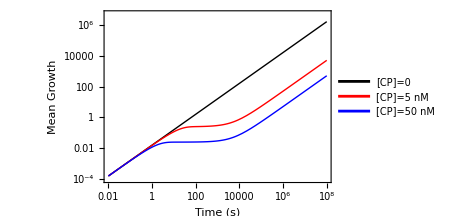
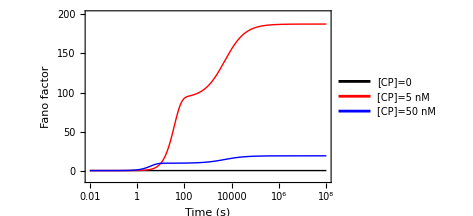
-Graphics- | -Graphics-

```mathematica
(*************************************** Plot ***************************************)
(*Off[General::munfl];*)
B=k+kc; A=k/B;

dlt=r (-((-1+A) ⅇ^(-B t) (-1+ⅇ^(B t)))/B+A t);
vt=r (((-1+A) ⅇ^(-2 B t) (-1+ⅇ^(B t)) (-1+A-ⅇ^(B t)+5 A ⅇ^(B t)) r)/B^2+A t-((-1+A) ⅇ^(-B t) (-1+2 (-1+2 A) r t+ⅇ^(B t) (1+2 A r t)))/B);
ft=vt/dlt;

kc=kcp*CP;

r=6;                  
k=2*10^-4;            
kcp=128*10^-4;        
scalingFactor=27/10000; 

(*Convert machine-precision k and kcp to high-precision*)
highPrecisionRules={k->SetPrecision[2*10^-4,30],kcp->SetPrecision[128*10^-4,30]};

(*Apply high precision to dlt0,dlt5,dlt50*)
dlt0=dlt/. {CP->0}/. highPrecisionRules;
dlt5=dlt/. {CP->5}/. highPrecisionRules;
dlt50=dlt/. {CP->50}/. highPrecisionRules;

ft0=ft/. {CP->0}/. highPrecisionRules;
ft5=ft/. {CP->5}/. highPrecisionRules;
ft50=ft/. {CP->50}/. highPrecisionRules;

ti=0.01; tf=10^8;
p1=LogLogPlot[{dlt0*scalingFactor,dlt5*scalingFactor,dlt50*scalingFactor},{t,ti,tf},WorkingPrecision->30,Frame->True,GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Time (s)","Mean Growth"},ImageSize->350,PlotLegends->{"[CP]=0","[CP]=5 nM", "[CP]=50 nM"},PlotRange->{{10^-2,10^8},{10^-4,5*10^6}}];

p2=LogLinearPlot[{ft0,ft5,ft50},{t,ti,tf},WorkingPrecision->30,Frame->True,GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Time (s)","Fano factor"},ImageSize->350,PlotLegends->{"[CP]=0","[CP]=5 nM", "[CP]=50 nM"},PlotRange->{{10^-2,10^8},{-10,200}}];

Grid[{{p1,p2}}]

Quit[];
```

```mathematica
(*************************************** Data export ***************************************)
Off[General::munfl];

Id=({{1, 0}, {0, 1}}); km=({{-kc, k}, {kc, -k}}); Iv=({{1}, {0}}); Ret=({{r, 0}, {0, 0}}); Rem=({{r, 0}}); (*Useful matrices*)

dlsv0=Inverse[(s*Id-km)].Iv; (*Subscript[ΔL^(->), s]^(0): Eq. S12 with x=0 *)
dlsv1=Inverse[(s*Id-km)].Ret.dlsv0; (*Subscript[ΔL^(->), s]^(1): Eq. S12 with x=1 *)

dls=1/s*Rem.dlsv0; (* <Subscript[ΔL, s]^1>: Eq. S8 with n=1 *)
dl2s=1/s*Rem.dlsv0+2/s*Rem.dlsv1; (* <Subscript[ΔL, s]^2>: Eq. S8 with n=2 *)

dltm=InverseLaplaceTransform[dls,s,t]; (* <Subscript[ΔL, t]>: Eq. S13 with n=1 *)
dl2tm=InverseLaplaceTransform[dl2s,s,t];(* <Subscript[ΔL, t]^2>: Eq. S13 with n=2 *)

dlt=dltm[[1,1]]; (* <Subscript[ΔL, t]> *)
dl2t=dl2tm[[1,1]]; (* <Subscript[ΔL, t]^2> *)
vt=dl2t-dlt^2; (* Variance *)
ft=vt/dlt;

kc=kcp*CP;

(*Common parameters*)
r=6; k=2*10^-4; kcp=12.8*10^-3;

(*Data Format*)
toEString[dat_]:=If[dat==0.,"0.0000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];

ti=0.01; 
tf1=0.1; tf2=1; tf3=10; tf4=100; tf5=1000; tf6=10000; tf7=100000; tf8=1000000; tf9=10000000; tf10=100000000;
dt1=0.0009; dt2=0.009; dt3=0.09; dt4=0.9; dt5=9; dt6=90; dt7=900; dt8=9000; dt9=90000; dt10=900000;

Clear[CP];
CP=0;
tb11=Table[{t,dlt*0.0027,ft},{t,ti,tf1,dt1}];
tb12=Table[{t,dlt*0.0027,ft},{t,tf1+dt2,tf2,dt2}];
tb13=Table[{t,dlt*0.0027,ft},{t,tf2+dt3,tf3,dt3}];
tb14=Table[{t,dlt*0.0027,ft},{t,tf3+dt4,tf4,dt4}];
tb15=Table[{t,dlt*0.0027,ft},{t,tf4+dt5,tf5,dt5}];
tb16=Table[{t,dlt*0.0027,ft},{t,tf5+dt6,tf6,dt6}];
tb17=Table[{t,dlt*0.0027,ft},{t,tf6+dt7,tf7,dt7}];
tb18=Table[{t,dlt*0.0027,ft},{t,tf7+dt8,tf8,dt8}];
tb19=Table[{t,dlt*0.0027,ft},{t,tf8+dt9,tf9,dt9}];
tb110=Table[{t,dlt*0.0027,ft},{t,tf9+dt10,tf10,dt10}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-CP-model\\GitHub\\t-dl-f-CP0.dat",tbp1,"FieldSeparators"->"    "];


Clear[CP];
CP=5;
tb21=Table[{t,dlt*0.0027,ft},{t,ti,tf1,dt1}];
tb22=Table[{t,dlt*0.0027,ft},{t,tf1+dt2,tf2,dt2}];
tb23=Table[{t,dlt*0.0027,ft},{t,tf2+dt3,tf3,dt3}];
tb24=Table[{t,dlt*0.0027,ft},{t,tf3+dt4,tf4,dt4}];
tb25=Table[{t,dlt*0.0027,ft},{t,tf4+dt5,tf5,dt5}];
tb26=Table[{t,dlt*0.0027,ft},{t,tf5+dt6,tf6,dt6}];
tb27=Table[{t,dlt*0.0027,ft},{t,tf6+dt7,tf7,dt7}];
tb28=Table[{t,dlt*0.0027,ft},{t,tf7+dt8,tf8,dt8}];
tb29=Table[{t,dlt*0.0027,ft},{t,tf8+dt9,tf9,dt9}];
tb210=Table[{t,dlt*0.0027,ft},{t,tf9+dt10,tf10,dt10}];
tb2=Join[tb21,tb22,tb23,tb24,tb25,tb26,tb27,tb28,tb29,tb210];
tbp2=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb2];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-CP-model\\GitHub\\t-dl-f-CP5.dat",tbp2,"FieldSeparators"->"    "];


Clear[CP];
CP=50;
tb31=Table[{t,dlt*0.0027,ft},{t,ti,tf1,dt1}];
tb32=Table[{t,dlt*0.0027,ft},{t,tf1+dt2,tf2,dt2}];
tb33=Table[{t,dlt*0.0027,ft},{t,tf2+dt3,tf3,dt3}];
tb34=Table[{t,dlt*0.0027,ft},{t,tf3+dt4,tf4,dt4}];
tb35=Table[{t,dlt*0.0027,ft},{t,tf4+dt5,tf5,dt5}];
tb36=Table[{t,dlt*0.0027,ft},{t,tf5+dt6,tf6,dt6}];
tb37=Table[{t,dlt*0.0027,ft},{t,tf6+dt7,tf7,dt7}];
tb38=Table[{t,dlt*0.0027,ft},{t,tf7+dt8,tf8,dt8}];
tb39=Table[{t,dlt*0.0027,ft},{t,tf8+dt9,tf9,dt9}];
tb310=Table[{t,dlt*0.0027,ft},{t,tf9+dt10,tf10,dt10}];
tb3=Join[tb31,tb32,tb33,tb34,tb35,tb36,tb37,tb38,tb39,tb310];
tbp3=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb3];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-CP-model\\GitHub\\t-dl-f-CP50.dat",tbp3,"FieldSeparators"->"    "];


Quit[];
```

# Long-time Limit

```mathematica
(*************************************** Analytical expressions ***************************************)

(*
Abbreviations:
k = k_C^- and kc = k_C^+
A = A_C and B = D_C
*)

k=A*B; kc=B-k;

Id=({{1, 0}, {0, 1}}); km=({{-kc, k}, {kc, -k}}); Iv=({{1}, {0}}); Ret=({{r, 0}, {0, 0}}); Rem=({{r, 0}});

dltv01=({{p1}, {p2}}); Y=({{1, 1}});
e1=km.dltv01; (*Eq (S14)*)
e2=Y.dltv01; (*Eq (S15)*)
eq1=e1[[1,1]]; eq2=e1[[2,1]]; eq3=e2[[1,1]];
sol=Solve[{eq1==0,eq3==1},{p1,p2}];
p11=p1/.sol[[1,1]];
p12=p2/.sol[[1,2]];

dltv0=({{p11}, {p12}});

dlsv1=1/s*Inverse[(s*Id-km)].Ret.dltv0; (*Subscript[ΔL^(->), s]^(1): Eq. S17 with x=1 *)

dls=1/s^2*Rem.dltv0; (* <Subscript[ΔL, s]^1>: Eq. S16 with n=1 *)
dl2s=1/s^2*Rem.dltv0+2/s*Rem.dlsv1; (* <Subscript[ΔL, s]^2>: Eq. S16 with n=2 *)

dltm=InverseLaplaceTransform[dls,s,t]; (* <Subscript[ΔL, t]>: Eq. S18 with n=1 *)
dl2tm=InverseLaplaceTransform[dl2s,s,t]; (* <Subscript[ΔL, t]^2>: Eq. S18 with n=2 *)

dlt=dltm[[1,1]]; (* <Subscript[ΔL, t]> *)
dl2t=dl2tm[[1,1]]; (* <Subscript[ΔL, t]^2> *)
vt=dl2t-dlt^2; (* Variance *)

FullSimplify[dlt]
FullSimplify[vt]

Quit[];
```

A r t

A r (t-(2 (-1+A) ⅇ^(-B t) r (1+ⅇ^(B t) (-1+B t)))/B^2)

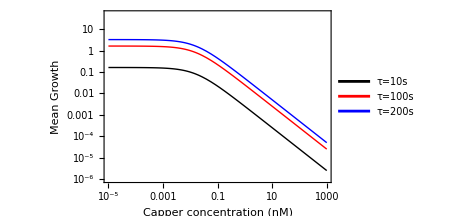
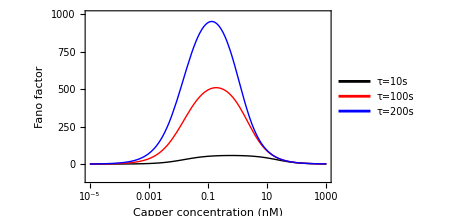
-Graphics- | -Graphics-

```mathematica
(*************************************** Plot ***************************************)
(*Off[General::munfl];*)
B=k+kc; A=k/B;

dlt=A r t;
vt=A r (t-(2 (-1+A) ⅇ^(-B t) r (1+ⅇ^(B t) (-1+B t)))/B^2);
ft=vt/dlt;

kc=kcp*CP;

r=6;                  
k=2*10^-4;            
kcp=128*10^-4;        
scalingFactor=27/10000; 

(*Convert machine-precision k and kcp to high-precision*)
highPrecisionRules={k->SetPrecision[2*10^-4,30],kcp->SetPrecision[128*10^-4,30]};

(*Apply high precision to dlt0,dlt5,dlt50*)
dlt10=dlt/. {t->10}/. highPrecisionRules;
dlt100=dlt/. {t->100}/. highPrecisionRules;
dlt200=dlt/. {t->200}/. highPrecisionRules;

ft10=ft/. {t->10}/. highPrecisionRules;
ft100=ft/. {t->100}/. highPrecisionRules;
ft200=ft/. {t->200}/. highPrecisionRules;

cpi=10^-5; cpf=10^3;
p1=LogLogPlot[{dlt10*scalingFactor,dlt100*scalingFactor,dlt200*scalingFactor},{CP,cpi,cpf},WorkingPrecision->30,Frame->True,GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Capper concentration (nM)","Mean Growth"},ImageSize->350,PlotLegends->{"τ=10s","τ=100s", "τ=200s"},PlotRange->{{10^-5,10^3},{10^-6,5*10^1}}];

p2=LogLinearPlot[{ft10,ft100,ft200},{CP,cpi,cpf},WorkingPrecision->30,Frame->True,GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Capper concentration (nM)","Fano factor"},ImageSize->350,PlotLegends->{"τ=10s","τ=100s", "τ=200s"},PlotRange->{{10^-5,10^3},{-100,1000}}];

Grid[{{p1,p2}}]

Quit[];
```

```mathematica
(*************************************** Data export ***************************************)
Off[General::munfl];

Id=({{1, 0}, {0, 1}}); km=({{-kc, k}, {kc, -k}}); Iv=({{1}, {0}}); Ret=({{r, 0}, {0, 0}}); Rem=({{r, 0}});

dltv01=({{p1}, {p2}}); Y=({{1, 1}});
e1=km.dltv01; (*Eq (S14)*)
e2=Y.dltv01; (*Eq (S15)*)
eq1=e1[[1,1]]; eq2=e1[[2,1]]; eq3=e2[[1,1]];
sol=Solve[{eq1==0,eq3==1},{p1,p2}];
p11=p1/.sol[[1,1]];
p12=p2/.sol[[1,2]];

dltv0=({{p11}, {p12}});

dlsv1=1/s*Inverse[(s*Id-km)].Ret.dltv0; (*Subscript[ΔL^(->), s]^(1): Eq. S17 with x=1 *)

dls=1/s^2*Rem.dltv0; (* <Subscript[ΔL, s]^1>: Eq. S16 with n=1 *)
dl2s=1/s^2*Rem.dltv0+2/s*Rem.dlsv1; (* <Subscript[ΔL, s]^2>: Eq. S16 with n=2 *)

dltm=InverseLaplaceTransform[dls,s,t]; (* <Subscript[ΔL, t]>: Eq. S18 with n=1 *)
dl2tm=InverseLaplaceTransform[dl2s,s,t]; (* <Subscript[ΔL, t]^2>: Eq. S18 with n=2 *)

dlt=dltm[[1,1]]; (* <Subscript[ΔL, t]> *)
dl2t=dl2tm[[1,1]]; (* <Subscript[ΔL, t]^2> *)
vt=dl2t-dlt^2; (* Variance *)
ft=vt/dlt;

kc=kcp*CP;

(*Common parameters*)
r=6; k=2*10^-4; kcp=12.8*10^-3;

toEString[dat_]:=If[dat==0.,"0.0000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];

CPi=10^-9;CPf1=10^-8;  CPf2=10^-7; CPf3=10^-6; CPf4=10^-5; CPf5=10^-4; CPf6=10^-3; CPf7=10^-2; CPf8=10^-1; CPf9=10^0; CPf10=10^1; CPf11=10^2; CPf12=10^3; CPf13=10^4;  CPf14=10^5; CPf15=10^6;
df1=0.9*10^-10; df2=0.9*10^-9; df3=0.9*10^-8; df4=0.9*10^-7; df5=0.9*10^-6; df6=0.9*10^-5; df7=0.9*10^-4; df8=0.9*10^-3; df9=0.9*10^-2; df10=0.9*10^-1; df11=0.9*10^0; df12=0.9*10^1; df13=0.9*10^2; df14=0.9*10^3; df15=0.9*10^4;

Clear[t];
t=10;
tb11=Table[{CP,dlt*0.0027,ft},{CP,CPi,CPf1,df1}];
tb12=Table[{CP,dlt*0.0027,ft},{CP,CPf1+df2,CPf2,df2}];
tb13=Table[{CP,dlt*0.0027,ft},{CP,CPf2+df3,CPf3,df3}];
tb14=Table[{CP,dlt*0.0027,ft},{CP,CPf3+df4,CPf4,df4}];
tb15=Table[{CP,dlt*0.0027,ft},{CP,CPf4+df5,CPf5,df5}];
tb16=Table[{CP,dlt*0.0027,ft},{CP,CPf5+df6,CPf6,df6}];
tb17=Table[{CP,dlt*0.0027,ft},{CP,CPf6+df7,CPf7,df7}];
tb18=Table[{CP,dlt*0.0027,ft},{CP,CPf7+df8,CPf8,df8}];
tb19=Table[{CP,dlt*0.0027,ft},{CP,CPf8+df9,CPf9,df9}];
tb110=Table[{CP,dlt*0.0027,ft},{CP,CPf9+df10,CPf10,df10}];
tb111=Table[{CP,dlt*0.0027,ft},{CP,CPf10+df11,CPf11,df11}];
tb112=Table[{CP,dlt*0.0027,ft},{CP,CPf11+df12,CPf12,df12}];
tb113=Table[{CP,dlt*0.0027,ft},{CP,CPf12+df13,CPf13,df13}];
tb114=Table[{CP,dlt*0.0027,ft},{CP,CPf13+df14,CPf14,df14}];
tb115=Table[{CP,dlt*0.0027,ft},{CP,CPf14+df15,CPf15,df15}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110,tb111,tb112,tb113,tb114,tb115];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-CP-model\\GitHub\\CP-dl-f-tau10.dat",tbp1,"FieldSeparators"->"    "];

Clear[t];
t=100;
tb11=Table[{CP,dlt*0.0027,ft},{CP,CPi,CPf1,df1}];
tb12=Table[{CP,dlt*0.0027,ft},{CP,CPf1+df2,CPf2,df2}];
tb13=Table[{CP,dlt*0.0027,ft},{CP,CPf2+df3,CPf3,df3}];
tb14=Table[{CP,dlt*0.0027,ft},{CP,CPf3+df4,CPf4,df4}];
tb15=Table[{CP,dlt*0.0027,ft},{CP,CPf4+df5,CPf5,df5}];
tb16=Table[{CP,dlt*0.0027,ft},{CP,CPf5+df6,CPf6,df6}];
tb17=Table[{CP,dlt*0.0027,ft},{CP,CPf6+df7,CPf7,df7}];
tb18=Table[{CP,dlt*0.0027,ft},{CP,CPf7+df8,CPf8,df8}];
tb19=Table[{CP,dlt*0.0027,ft},{CP,CPf8+df9,CPf9,df9}];
tb110=Table[{CP,dlt*0.0027,ft},{CP,CPf9+df10,CPf10,df10}];
tb111=Table[{CP,dlt*0.0027,ft},{CP,CPf10+df11,CPf11,df11}];
tb112=Table[{CP,dlt*0.0027,ft},{CP,CPf11+df12,CPf12,df12}];
tb113=Table[{CP,dlt*0.0027,ft},{CP,CPf12+df13,CPf13,df13}];
tb114=Table[{CP,dlt*0.0027,ft},{CP,CPf13+df14,CPf14,df14}];
tb115=Table[{CP,dlt*0.0027,ft},{CP,CPf14+df15,CPf15,df15}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110,tb111,tb112,tb113,tb114,tb115];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-CP-model\\GitHub\\CP-dl-f-tau100.dat",tbp1,"FieldSeparators"->"    "];

Clear[t];
t=200;
tb11=Table[{CP,dlt*0.0027,ft},{CP,CPi,CPf1,df1}];
tb12=Table[{CP,dlt*0.0027,ft},{CP,CPf1+df2,CPf2,df2}];
tb13=Table[{CP,dlt*0.0027,ft},{CP,CPf2+df3,CPf3,df3}];
tb14=Table[{CP,dlt*0.0027,ft},{CP,CPf3+df4,CPf4,df4}];
tb15=Table[{CP,dlt*0.0027,ft},{CP,CPf4+df5,CPf5,df5}];
tb16=Table[{CP,dlt*0.0027,ft},{CP,CPf5+df6,CPf6,df6}];
tb17=Table[{CP,dlt*0.0027,ft},{CP,CPf6+df7,CPf7,df7}];
tb18=Table[{CP,dlt*0.0027,ft},{CP,CPf7+df8,CPf8,df8}];
tb19=Table[{CP,dlt*0.0027,ft},{CP,CPf8+df9,CPf9,df9}];
tb110=Table[{CP,dlt*0.0027,ft},{CP,CPf9+df10,CPf10,df10}];
tb111=Table[{CP,dlt*0.0027,ft},{CP,CPf10+df11,CPf11,df11}];
tb112=Table[{CP,dlt*0.0027,ft},{CP,CPf11+df12,CPf12,df12}];
tb113=Table[{CP,dlt*0.0027,ft},{CP,CPf12+df13,CPf13,df13}];
tb114=Table[{CP,dlt*0.0027,ft},{CP,CPf13+df14,CPf14,df14}];
tb115=Table[{CP,dlt*0.0027,ft},{CP,CPf14+df15,CPf15,df15}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110,tb111,tb112,tb113,tb114,tb115];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-CP-model\\GitHub\\CP-dl-f-tau200.dat",tbp1,"FieldSeparators"->"    "];

Quit[];
```

General::munfl: 7.2602×10^-305 0.000108412 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.80225×10^-306)/5000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.522] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1395.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1510.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1625.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-13952.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15104.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-16256.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.7701×10^-306)/5000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.06] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1395.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1510.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1625.62] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-13952.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15104.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-16256.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-139520.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-151040.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-162560.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-716.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-739.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-762.92] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2790.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3020.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3251.24] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-27904.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-30208.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-32512.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-279040.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-302080.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-325120.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.